# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,maxran_,limit_,label_,epilog_:{}]:=Module[{funplot,epsplot},
funplot=DiscretePlot[fun[n],{n,0,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{0,limit},{maxran,limit}}],Arrow[{{(*maxran-20*)20,limit+.05},{(*maxran-25*)15,limit}}],Text["lim_(n → ∞) a_n="<>ToString[limit],{(*maxran-20*)22,limit+.05},Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,.2},0.0001,.2,Appearance->"Open" }
]
]*)
```

# 1) Elektrisches Netzwerk II

a) Setting 1
(U_a
I_a)=P_1(R)·(U_e
I_e),       P_1(R)=?

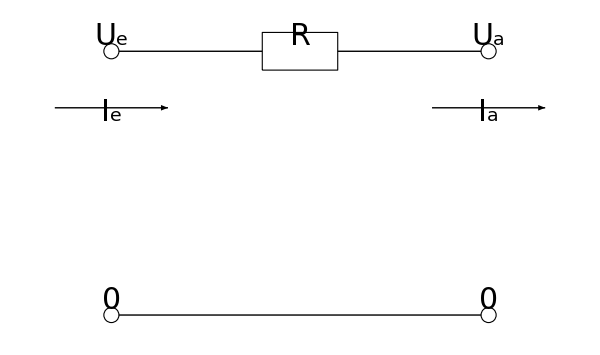

```mathematica
left=-1;
right=1;
upper=.7;
lower=-.7;
center=0;

ptUL={left,upper};
ptUR={right,upper};
ptDL={left,lower};
ptDR={right,lower};
ptUC={center,upper};
ptDC={center,lower};

whiteDot[pt_,rad_:.04]:={PointSize[.03],White,EdgeForm[Black],Disk[pt,rad]};
label[text_,pt_]:=Text[Style[TraditionalForm@text,30,Italic,FontFamily->"Times New Roman"],pt,{0,-3}]
resistor[pt_]:={White,EdgeForm[Black],Rectangle@@({pt+{-.2,-.1},pt+{.2,.1}})}
arrow[pt_]:={Arrow[{pt+{-.3,-.3},pt+{.3,-.3}}]};

Framed@Graphics[{Line[{{ptUL,ptUR},{ptDL,ptDR}}],{whiteDot[ptUL],whiteDot[ptUR],whiteDot[ptDL],whiteDot[ptDR]},
{arrow[ptUL],arrow[ptUR]},
resistor[ptUC],{label["U_e",ptUL],label["U_a",ptUR],label["0",ptDL],label["0",ptDR],label["R",ptUC],label["I_e",ptUL+{0,-.4}],label["I_a",ptUR+{0,-.4}]}},ImageSize->600]
```

b) Setting 2
(U_a
I_a)=P_2(R)·(U_e
I_e),       P_2(R)=?

```mathematica
Framed@Graphics[{Line[{{ptUL,ptUR},{ptDL,ptDR},{ptUC,ptDC}}],{PointSize[.03],Point[{ptUC,ptDC}]},{whiteDot[ptUL],whiteDot[ptUR],whiteDot[ptDL],whiteDot[ptDR]},
{arrow[ptUL],arrow[ptUR]},Rotate[resistor[(ptUC+ptDC)/2],π/2],{label["U_e",ptUL],label["U_a",ptUR],label["0",ptDL],label["0",ptDR],label["R",(ptUC+ptDC)/2+{.3,-.2}],label["I_e",ptUL+{0,-.4}],label["I_a",ptUR+{0,-.4}]}},ImageSize->600]
```

-Graphics-

c) Together
A = P_1(R_3)·P_2(R_2)·P_1(R_1) = ?

## Solution

## a)

From the propositions (see Übungen from the last week):

I_a=I_e
U_e-U_a=R·I_e  ⇒  U_a=U_e-R·I_e

And so:

P_1(R)=(1 | -R
0 | 1)

## b)

From the propositions (see Übungen from the last week):

U_a=U_e
U_e=R·I_2  ⇒  I_2=U_e/R
I_e=I_a+I_2  ⇒ I_a=I_e-U_e/R

And so:

P_2(R)=(1 | 0
-1/R | 1)

## c)

A = P_1(R_3)·P_2(R_2)·P_1(R_1) =(1 | -R_3
0 | 1)·(1 | 0
-1/R_2 | 1)·(1 | -R_1
0 | 1)=1/R_2(R_2+R_3 | -(R_1 R_2+R_2 R_3+R_1 R_3)
-1 | R_2+R_1)

It is exactly the matrix we considered last week in Übung 6.1.

# 2) Beinahe-Inversion

D: 𝒞^∞(ℝ)→𝒞^∞(ℝ)
                f↦f'

S: 𝒞^∞(ℝ)→𝒞^∞(ℝ)
                f↦S f
                (S f)(x):=∫_0^x f(y)ⅆy

a) Ker D = ?, Ker S = ?

b) D ◦ S = 𝕀𝕕 ?

c) P:=S ◦ D ≠ 𝕀𝕕 ?

d) Im(𝕀𝕕-P) = ?

## Solution

## a)

### Operation D

Ker D={f∈𝒞^∞(ℝ)|f'=0}, i.e. f'(x)=0 for all x∈ℝ

f'(x)=0  ⇒  f(x)=c    for some constant  c∈ℝ

The kernel of D is therefore composed of constant functions:

Ker D = {f∈𝒞^∞(ℝ)|∃c∈ℝ:∀x∈ℝ: f(x)=c}

### Operation S

Ker S={f∈𝒞^∞(ℝ)|∀x∈ℝ:∫_0^x f(y)ⅆy=0}

But ∫_0^x f(y)ⅆy=F(x)-F(0) (Newton-Leibniz formula), where F(x)=∫_0^x f(y)ⅆy. And so for all x∈ℝ we have F(x)-F(0)=0 and F is therefore a constant function: F(x)=F(0)=c∈ℝ. The derivative of a constant function is zero and so F'(x)≡f(x)=0. All functions f from the kernel are thus zero function(s):

Ker S = {0_f}, where 0_f is a function satisfying 0_f(x)=0 for all x∈ℝ.

## b)

(D ◦ S)(f)(x)=D(S(f))(x)=D(∫_0^x f(y)ⅆy)=f(x) and so (D ◦ S)(f)=f

## c)

Differentiation D transforms all constant functions into the zero function. Thus for a non-zero constant function f(x)=c>0 we get:

P(f)=S(D(f))=S(0_f)=0_f≠ f

## d)

See c). All functions that differ only by an additive constant are transformed into the same function after application of P. Let f∈𝒞^∞(ℝ) be an arbitrary function. Then (in the second equality we used again the Newton-Leibniz formula):

(𝕀𝕕-P)(f)(x)=f(x)-S(f')(x)=f(x)-(f(x)-f(0))=f(0)

So for any function f, its image under (𝕀𝕕-P) is a function, that for any x∈ℝ returns a constant number f(0). Therefore:

Im(𝕀𝕕-P) = {f∈𝒞^∞(ℝ)|∃c∈ℝ:∀x∈ℝ: f(x)=c}

# 3) Matrixinversion

A_1=(0 | 1 | -2 | 2
-2 | -2 | 7 | -7
4 | 1 | -8 | 9
1 | 0 | -1 | 1), A_2=(1 | 0 | 3 | -4
1 | 2 | 1 | -2
2 | 0 | 1 | -1
2 | 1 | 0 | 0), A_3=(1 | ⅈ | 0
0 | -ⅈ | 1
1-ⅈ | 0 | 1)

a) Invertible?

b) Inverse matrices?

## Solution

## A_1

Gaussian elimination of extended A_1:

(A_1|𝕀𝕕)=(0 | 1 | -2 | 2
-2 | -2 | 7 | -7
4 | 1 | -8 | 9
1 | 0 | -1 | 11 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)∼(1 | 0 | -1 | 1
0 | -2 | 5 | -5
0 | 1 | -2 | 2
0 | 1 | -4 | 50 | 0 | 0 | 1
0 | 1 | 0 | 2
1 | 0 | 0 | 0
0 | 0 | 1 | -4)∼(1 | 0 | -1 | 1
0 | 1 | -2 | 2
0 | 0 | -2 | 3
0 | 0 | 1 | -10 | 0 | 0 | 1
1 | 0 | 0 | 0
-1 | 0 | 1 | -4
2 | 1 | 0 | 2)∼(1 | 0 | -1 | 1
0 | 1 | -2 | 2
0 | 0 | 1 | -1
0 | 0 | 0 | 10 | 0 | 0 | 1
1 | 0 | 0 | 0
2 | 1 | 0 | 2
3 | 2 | 1 | 0)∼(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 12 | 1 | 0 | 3
5 | 2 | 0 | 4
5 | 3 | 1 | 2
3 | 2 | 1 | 0)

The final matrix is of the form (𝕀𝕕|B_1). As rank(𝕀𝕕) is maximal matrix A_1 is invertible and A_1^-1=B_1=(2 | 1 | 0 | 3
5 | 2 | 0 | 4
5 | 3 | 1 | 2
3 | 2 | 1 | 0).

## A_2

Gaussian elimination of extended A_2:

(A_2|𝕀𝕕)=(1 | 0 | 3 | -4
1 | 2 | 1 | -2
2 | 0 | 1 | -1
2 | 1 | 0 | 01 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)∼(1 | 0 | 3 | -4
0 | 2 | -2 | 2
0 | 0 | -5 | 7
0 | 1 | -6 | 81 | 0 | 0 | 0
-1 | 1 | 0 | 0
-2 | 0 | 1 | 0
-2 | 0 | 0 | 1)∼(1 | 0 | 3 | -4
0 | 1 | -6 | 8
0 | 0 | 10 | -14
0 | 0 | -5 | 71 | 0 | 0 | 0
-2 | 0 | 0 | 1
3 | 1 | 0 | -2
-2 | 0 | 1 | 0)∼(1 | 0 | 3 | -4
0 | 1 | -6 | 8
0 | 0 | -5 | 7
0 | 0 | 0 | 01 | 0 | 0 | 0
-2 | 0 | 0 | 1
-2 | 0 | 1 | 0
-1 | 1 | 2 | -2)

The rank of the matrix on the left-hand side is equal to 3, which is strictly smaller than the number of rows. The matrix is therefore NOT invertible.

## A_3

Gaussian elimination of extended A_3:

(A_3|𝕀𝕕)=(1 | ⅈ | 0 | 1 | 0 | 0
0 | -ⅈ | 1 | 0 | 1 | 0
1-ⅈ | 0 | 1 | 0 | 0 | 1)∼(1 | ⅈ | 0 | 1 | 0 | 0
0 | 1 | ⅈ | 0 | ⅈ | 0
0 | -1-ⅈ | 1 | -1+ⅈ | 0 | 1)∼(1 | ⅈ | 0 | 1 | 0 | 0
0 | 1 | ⅈ | 0 | ⅈ | 0
0 | 0 | ⅈ | -1+ⅈ | -1+ⅈ | 1)∼(1 | ⅈ | 0 | 1 | 0 | 0
0 | 1 | ⅈ | 0 | ⅈ | 0
0 | 0 | 1 | 1+ⅈ | 1+ⅈ | -ⅈ)∼(1 | ⅈ | 0 | 1 | 0 | 0
0 | 1 | 0 | 1-ⅈ | 1 | -1
0 | 0 | 1 | 1+ⅈ | 1+ⅈ | -ⅈ)∼(1 | 0 | 0 | -ⅈ | -ⅈ | ⅈ
0 | 1 | 0 | 1-ⅈ | 1 | -1
0 | 0 | 1 | 1+ⅈ | 1+ⅈ | -ⅈ)

The final matrix is of the form (𝕀𝕕|B_3). As rank(𝕀𝕕) is maximal matrix A_3 is invertible and A_3^-1=B_3=(-ⅈ | -ⅈ | ⅈ
1-ⅈ | 1 | -1
1+ⅈ | 1+ⅈ | -ⅈ).